```mathematica
q=.; k=.;
r=I*(q^2-k^2)*Sin[q*a]/(2*k*q*Cos[q*a]-I*(q^2+k^2)*Sin[q*a])
```

(ⅈ (-k^2+q^2) Sin[a q])/(2 k q Cos[a q]-ⅈ (k^2+q^2) Sin[a q])

```mathematica
R=FullSimplify[ComplexExpand[Abs[r]^2]]
```

(2 (k^2-q^2)^2 Sin[a q]^2)/(k^4+6 k^2 q^2+q^4-(k^2-q^2)^2 Cos[2 a q])

```mathematica
T=FullSimplify[Together[1-R]]
```

(8 k^2 q^2)/(k^4+6 k^2 q^2+q^4-(k^2-q^2)^2 Cos[2 a q])

```mathematica
Te = FullSimplify[T/.q -> Sqrt[2*m*(En-U)/h^2]/.k ->  Sqrt[2*m*En/h^2]]
```

(8 En (En-U))/(8 En^2-8 En U+U^2-U^2 Cos[2 √2 a √((m (En-U))/h^2)])

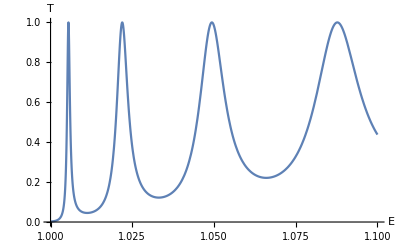

```mathematica
Plot[Te/.U->1/.m->1/.a->30/.h->1, {En, 1, 1.1}, ImageSize->Full, AxesLabel->{"E", "T"}]
```

```mathematica
Tk = FullSimplify[T/.k-> Sqrt[q^2+2*m*U/h^2]]
```

(2 h^2 q^2 (h^2 q^2+2 m U))/(2 h^4 q^4+4 h^2 m q^2 U+m^2 U^2-m^2 U^2 Cos[2 a q])

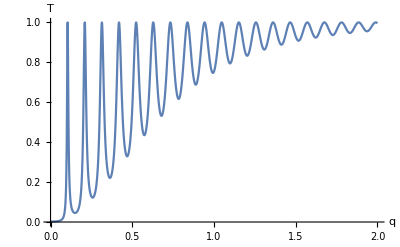

```mathematica
Plot[Tk/.U->1/.m->1/.a->30/.h->1, {q, 0, 2}, ImageSize->Full, AxesLabel->{"q", "T"}]
```

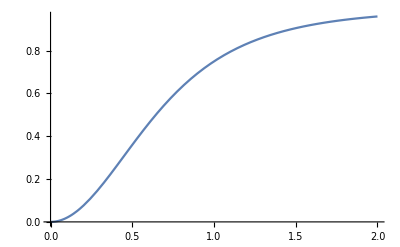

```mathematica
Plot[q^2*(q^2+al)/(q^4+al*q^2+al^2/4)/.al->2, {q, 0, 2}]
```

```mathematica
q^2[q^2+al]/(q^4+al*q^2+al^2/4)/.al->2
```

(q^(2[2+q^2]))/(1+2 q^2+q^4)